```mathematica
ClearAll["`*"]
```

### In this notebook, we will attempt to find out why Minimize and NMinimize produce conflicting results, and then have them produce the same results

```mathematica
ρ[a_][xi_]:=Sum[a[[i+1]] xi^i,{i,0,Length[a]-1}]
σ[b_][xi_]:=Sum[b[[i+1]] xi^i,{i,0,Length[b]-1}]
```

### Scenario 1: 2-step LMMs (all β coefficients are nonzero)

```mathematica
cond2step=((-1+2 β2) (-2+β1+2 β2)≤0&&((4 β2 (-2+β1+3 β2)>β1^2&&β1+2 β2≠2)||2+(-2+β1) β1≥4 β2^2)&&β1+2 β2>1)&&(Abs[β2 κ^2]>Abs[β0]&&Abs[β0^2-β2^2 κ^4]>Abs[β1 κ (β0-β2 κ^2)])/.{β0->-2+β1+3 β2}//Simplify;
```

#### Let’s see if we can fix the numerical issue via Reduce

```mathematica
trial=Reduce[{cond2step},{β1,β2},Reals]//Simplify;
```

```mathematica
c3[a_,b_]:=Abs[1/(σ[b][1])Sum[(j^3 a[[j+1]])/(3!)-(j^(3-1)b[[j+1]])/((3-1)!),{j,0,Length[a]-1}]]
```

```mathematica
c3[{3-2 β1-4 β2,-4+2 β1+4 β2,1},{-2+β1+3 β2,β1,β2}]//Simplify
```

1/12 Abs[(-4+β1+8 β2)/(-1+β1+2 β2)]

```mathematica
c32step[β1_,β2_]:=1/12 Abs[(-4+β1+8 β2)/(-1+β1+2 β2)]
```

```mathematica
1/12 Abs[(-4+β1+8 β2)/(-1+β1+2 β2)]//TeXForm
```

\frac{1}{12} \left| \frac{\text{$\beta $1}+8 \text{$\beta $2}-4}{\text{$\beta $1}+2 \text{$\beta $2}-1}\right|

#### Because Mathematica can’t handle plotting this directly, we will just make a table and sample points from κ=0 to 1

```mathematica
κlist2=Table[{k,Quiet[Minimize[{c32step[β1,β2],cond2step/. κ->k},{β1,β2}][[1]]]},{k,0,1,1/100}];
```

#### Because κ!=0, we will artificially add that in, as it corresponds to the BDF2 method

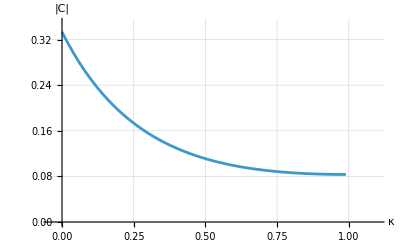

```mathematica
plt3=Plot[Quiet[NMinimize[{c32step[β1,β2],trial/.κ->k},{β1,β2}][[1]]],{k,0.00001,.99},AxesLabel->{κ, "|C|"},LabelStyle->Directive[FontSize->14],PlotRange->{{-0.04,1.1},{0,0.35}},GridLines->Automatic]
```

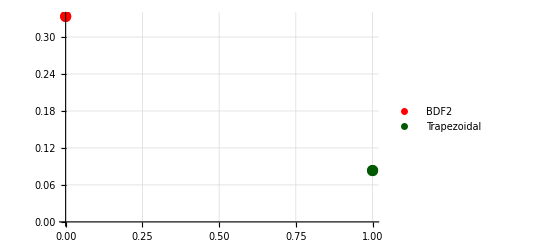

```mathematica
plt2=ListPlot[{{{0,1/3}},{{1,1/12}}},PlotLegends->{"BDF2","Trapezoidal"},LabelStyle->Directive[FontSize->14],PlotStyle->{{PointSize[.02],Red},{PointSize[.02],DarkGreen}},GridLines->Automatic]
```

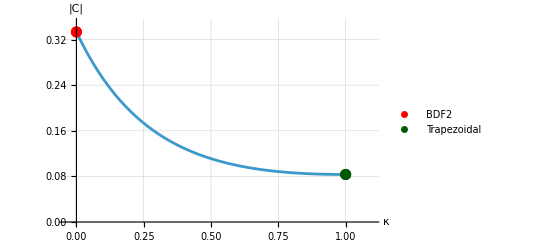

```mathematica
plt4=Show[plt3,plt2]
```

```mathematica
κlist2=κlist2/.κlist2[[1,2]]->1/3;
```

```mathematica
SetDirectory["C:\\Users\\Tyler Jensen\\Downloads"]
```

C:\Users\Tyler Jensen\Downloads

```mathematica
Export["perito_optimal_2step.pdf",plt4]
```

perito_optimal_2step.pdf

#### We now plot the analytical result below

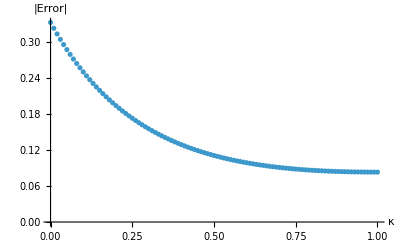

```mathematica
l1=ListPlot[κlist2,AxesLabel->{κ, "|Error|"}]
```

#### We now show the numerical result

```mathematica
NMinimize[{c32step[β1,β2],trial/. κ->2/3},{β1,β2}]
```

{0.0933333,{β1→0.685714,β2→0.514286}}

```mathematica
Clear[κlist3]
```

```mathematica
κlist3=Table[{k,Quiet[NMinimize[{c32step[β1,β2],trial/. κ->k},{β1,β2}]][[1]]},{k,0,1,.01}];
```

```mathematica
κlist3=κlist3/.κlist3[[1,2]]->N[1/3];
```

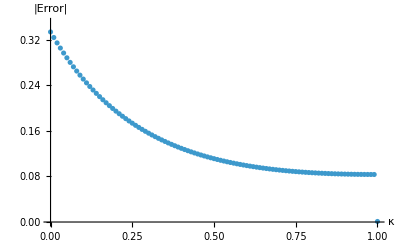

```mathematica
ListPlot[κlist3,AxesLabel->{κ, "|Error|"},PlotRange->{{0,1},{0,0.35}}]
```

#### It seems the key here was to use Reduce, let’s try it on the other set

### Scenario 2: 3-step LMMs (2 nonzero β coefficients)

```mathematica
ClearAll["`*"]
```

```mathematica
c32beta[β2_,β3_]:=Module[
{a,b,sum},
a={-1+β2/2+(3 β3)/2,3-2 β2-4 β3,-3+(3 β2)/2+(5 β3)/2,1};
b={0,0,β2,β3};
sum=Abs[1/(σ[b][1])Sum[(j^3 a[[j+1]])/(3!)-(j^(3-1)b[[j+1]])/((3-1)!),{j,0,Length[a]-1}]];
sum//Simplify
]
```

```mathematica
cond2beta=((β3==1/2&&β2==1/2)||(1/2<β3<3/5&&1/2 (2-5 β3)+1/2 √(4+4 β3-15 β3^2)≤β2≤β3)||(β3==3/5&&0≤β2≤3/5)||(3/5<β3<2/3&&1/2 (2-5 β3)+1/2 √(4+4 β3-15 β3^2)≤β2≤β3)||(β3==2/3&&β2≥-2/3)||(2/3<β3<1&&-β3≤β2≤2-2 β3)||(β3==1&&-1≤β2≤0)||(1<β3<2&&-β3≤β2≤2-2 β3)||(β3==2&&β2==-2))&&Abs[β3 κ]^2>Abs[β2 β3 κ];
```

```mathematica
(cond2beta//LogicalExpand)/.{β3->Subscript[β, 3],β2->Subscript[β, 2]}
```

```mathematica
(Subscript[β, 2]==-2&&Subscript[β, 3]==2&&Abs[κ Subscript[β, 3]]^2>Abs[κ Subscript[β, 2] Subscript[β, 3]])||(Subscript[β, 2]==1/2&&Subscript[β, 3]==1/2&&Abs[κ Subscript[β, 3]]^2>Abs[κ Subscript[β, 2] Subscript[β, 3]])||(Subscript[β, 3]==2/3&&Abs[κ Subscript[β, 3]]^2>Abs[κ Subscript[β, 2] Subscript[β, 3]]&&Subscript[β, 2]≥-2/3)||(Subscript[β, 3]==3/5&&Abs[κ Subscript[β, 3]]^2>Abs[κ Subscript[β, 2] Subscript[β, 3]]&&0≤Subscript[β, 2]&&Subscript[β, 2]≤3/5)||(Subscript[β, 3]==1&&Abs[κ Subscript[β, 3]]^2>Abs[κ Subscript[β, 2] Subscript[β, 3]]&&-1≤Subscript[β, 2]&&Subscript[β, 2]≤0)||(Abs[κ Subscript[β, 3]]^2>Abs[κ Subscript[β, 2] Subscript[β, 3]]&&1/2<Subscript[β, 3]&&Subscript[β, 3]<3/5&&Subscript[β, 2]≤Subscript[β, 3]&&1/2 (2-5 Subscript[β, 3])+1/2 √(4+4 Subscript[β, 3]-15 Subscript[β, 3]^2)≤Subscript[β, 2])||(Abs[κ Subscript[β, 3]]^2>Abs[κ Subscript[β, 2] Subscript[β, 3]]&&3/5<Subscript[β, 3]&&Subscript[β, 3]<2/3&&Subscript[β, 2]≤Subscript[β, 3]&&1/2 (2-5 Subscript[β, 3])+1/2 √(4+4 Subscript[β, 3]-15 Subscript[β, 3]^2)≤Subscript[β, 2])||(Abs[κ Subscript[β, 3]]^2>Abs[κ Subscript[β, 2] Subscript[β, 3]]&&2/3<Subscript[β, 3]&&Subscript[β, 3]<1&&Subscript[β, 2]≤2-2 Subscript[β, 3]&&-Subscript[β, 3]≤Subscript[β, 2])||(Abs[κ Subscript[β, 3]]^2>Abs[κ Subscript[β, 2] Subscript[β, 3]]&&1<Subscript[β, 3]&&Subscript[β, 3]<2&&Subscript[β, 2]≤2-2 Subscript[β, 3]&&-Subscript[β, 3]≤Subscript[β, 2])//TeXForm
```

\left(\beta _2=-2\land \beta _3=2\land \left| \kappa  \beta _3\right| {}^2>\left| \kappa  \beta _2 \beta _3\right| \right)\lor \left(\beta
   _2=\frac{1}{2}\land \beta _3=\frac{1}{2}\land \left| \kappa  \beta _3\right| {}^2>\left| \kappa  \beta _2 \beta _3\right| \right)\lor
   \left(\beta _3=\frac{2}{3}\land \left| \kappa  \beta _3\right| {}^2>\left| \kappa  \beta _2 \beta _3\right| \land \beta _2\geq
   -\frac{2}{3}\right)\lor \left(\beta _3=\frac{3}{5}\land \left| \kappa  \beta _3\right| {}^2>\left| \kappa  \beta _2 \beta _3\right| \land
   0\leq \beta _2\land \beta _2\leq \frac{3}{5}\right)\lor \left(\beta _3=1\land \left| \kappa  \beta _3\right| {}^2>\left| \kappa  \beta _2
   \beta _3\right| \land -1\leq \beta _2\land \beta _2\leq 0\right)\lor \left(\left| \kappa  \beta _3\right| {}^2>\left| \kappa  \beta _2 \beta
   _3\right| \land \frac{1}{2}<\beta _3\land \beta _3<\frac{3}{5}\land \beta _2\leq \beta _3\land \frac{1}{2} \left(2-5 \beta
   _3\right)+\frac{1}{2} \sqrt{-15 \beta _3^2+4 \beta _3+4}\leq \beta _2\right)\lor \left(\left| \kappa  \beta _3\right| {}^2>\left| \kappa 
   \beta _2 \beta _3\right| \land \frac{3}{5}<\beta _3\land \beta _3<\frac{2}{3}\land \beta _2\leq \beta _3\land \frac{1}{2} \left(2-5 \beta
   _3\right)+\frac{1}{2} \sqrt{-15 \beta _3^2+4 \beta _3+4}\leq \beta _2\right)\lor \left(\left| \kappa  \beta _3\right| {}^2>\left| \kappa 
   \beta _2 \beta _3\right| \land \frac{2}{3}<\beta _3\land \beta _3<1\land \beta _2\leq 2-2 \beta _3\land -\beta _3\leq \beta _2\right)\lor
   \left(\left| \kappa  \beta _3\right| {}^2>\left| \kappa  \beta _2 \beta _3\right| \land 1<\beta _3\land \beta _3<2\land \beta _2\leq 2-2
   \beta _3\land -\beta _3\leq \beta _2\right)

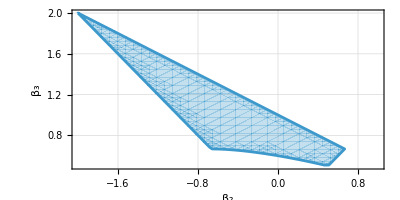

```mathematica
plt5=RegionPlot[cond2beta/.κ->1,{β2,-2,1},{β3,1/2,2},AspectRatio->1/2,Frame->True,FrameLabel->{Subscript[β, 2], Subscript[β, 3]},LabelStyle->Directive[FontSize->12],RotateLabel->False,GridLines->Automatic]
```

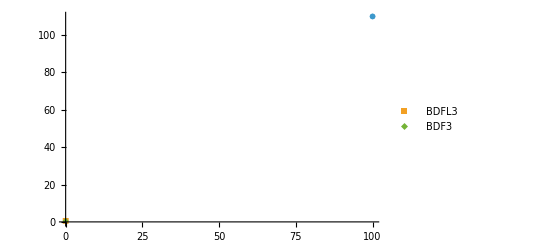

```mathematica
plt6=ListPlot[{{{100,110}},{{0,3/5}},{{0,6/11}}}/. {x_,y_}:>{x,y},PlotMarkers->{{Automatic,0.04},{Automatic,0.05},{Automatic,0.05}},PlotLegends->{None,"BDFL3","BDF3"}]
```

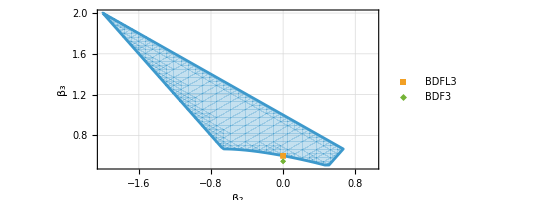

```mathematica
plt7=Show[plt5,plt6]
```

```mathematica
Export["3step_b2b3_examples.pdf",plt7]
```

3step_b2b3_examples.pdf

```mathematica
κlist=Table[{k,Quiet[Minimize[{c32beta[β2,β3],cond2beta/. κ->k},{β2,β3}][[1]]]},{k,0,1,1/100}];
```

#### Again we artificially add the first point where κ=0

```mathematica
κlist=κlist/.κlist[[1,2]]->1/6;
```

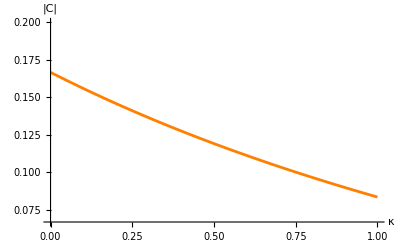

```mathematica
l2=ListLinePlot[κlist,AxesLabel->{κ, "|C|"},PlotRange->{{0,1},{1/15,1/5}},PlotStyle->Orange,LabelStyle->Directive[FontSize->14]]
```

```mathematica
Export["3step_b2b3_examples_sc.pdf",l2]
```

3step_b2b3_examples_sc.pdf

#### Let’s now try Reduce for NMinimize

```mathematica
trial2=Reduce[{cond2beta},{β2,β3},Reals]//Simplify;
```

```mathematica
Clear[κlist3b]
```

```mathematica
κlist3b=Table[{k,Quiet[NMinimize[{c32beta[β2,β3],trial2/. κ->k},{β2,β3},Method->"SimulatedAnnealing"][[1]]]},{k,0,1,.01}];
```

#### Simulated Annealing was chosen because it produced the most accurate results

```mathematica
κlist3b=κlist3b/.κlist3b[[1,2]]->1/6;
```

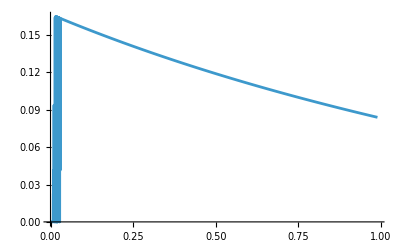

```mathematica
Plot[Quiet[NMinimize[{c32beta[β2,β3],trial2/. κ->k},{β2,β3},Method->"SimulatedAnnealing"][[1]]],{k,0.0001,.99}]
```

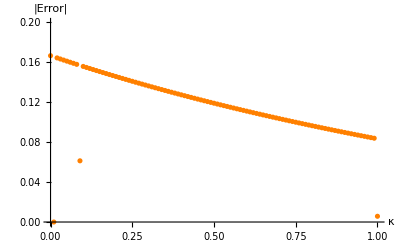

```mathematica
ListPlot[κlist3b,AxesLabel->{κ, "|Error|"},PlotRange->{{0,1},{0,1/5}},PlotStyle->Orange]
```

### Again, β_1 and β_3 are nonzero

```mathematica
cond2beta2=((Subscript[β, 1]>0&&Subscript[β, 3]≥0&&((Subscript[β, 1]+Subscript[β, 3]>0&&√(9-2 Subscript[β, 1]+9 Subscript[β, 1]^2)+10 Subscript[β, 3]≤3+3 Subscript[β, 1]&&((Subscript[β, 1]≤3&&Subscript[β, 3]≤1)||(3<Subscript[β, 1]<16&&8 (1+√(1+5 Subscript[β, 1]))>5 (Subscript[β, 1]+5 Subscript[β, 3]))))||(Subscript[β, 1]<1&&3+3 Subscript[β, 1]+√(9-2 Subscript[β, 1]+9 Subscript[β, 1]^2)≤10 Subscript[β, 3]&&Subscript[β, 3]≤1)))||(Subscript[β, 3]≤1&&((3+3 Subscript[β, 1]+√(9-2 Subscript[β, 1]+9 Subscript[β, 1]^2)≤10 Subscript[β, 3]&&((Subscript[β, 1]==0&&Subscript[β, 3]>0)||(-1/2<Subscript[β, 1]<0&&Subscript[β, 1]+Subscript[β, 3]≥0)))||(-1<Subscript[β, 1]≤-1/2&&Subscript[β, 1]+Subscript[β, 3]>0))))&&(Abs[κ^6 Subscript[β, 3]^2]>Abs[κ^4 Subscript[β, 1] Subscript[β, 3]]&&Abs[κ^8 Subscript[β, 3]^2 (Subscript[β, 1]^2-κ^4 Subscript[β, 3]^2)]>0)/.{Subscript[β, 1]->β1,Subscript[β, 3]->β3}//Simplify;
```

```mathematica
(cond2beta2//LogicalExpand)/.{β1->Subscript[β, 1],β3->Subscript[β, 3]}
```

```mathematica
(Subscript[β, 1]==0&&Subscript[β, 3]>0&&Abs[κ^6 Subscript[β, 3]^2]>Abs[κ^4 Subscript[β, 1] Subscript[β, 3]]&&Abs[κ^8 Subscript[β, 3]^2 (Subscript[β, 1]^2-κ^4 Subscript[β, 3]^2)]>0&&3+3 Subscript[β, 1]+√(9-2 Subscript[β, 1]+9 Subscript[β, 1]^2)≤10 Subscript[β, 3]&&Subscript[β, 3]≤1)||(Subscript[β, 1]+Subscript[β, 3]>0&&Abs[κ^6 Subscript[β, 3]^2]>Abs[κ^4 Subscript[β, 1] Subscript[β, 3]]&&Abs[κ^8 Subscript[β, 3]^2 (Subscript[β, 1]^2-κ^4 Subscript[β, 3]^2)]>0&&-1<Subscript[β, 1]&&Subscript[β, 1]≤-1/2&&Subscript[β, 3]≤1)||(Subscript[β, 1]>0&&Abs[κ^6 Subscript[β, 3]^2]>Abs[κ^4 Subscript[β, 1] Subscript[β, 3]]&&Abs[κ^8 Subscript[β, 3]^2 (Subscript[β, 1]^2-κ^4 Subscript[β, 3]^2)]>0&&Subscript[β, 3]≥0&&Subscript[β, 1]<1&&3+3 Subscript[β, 1]+√(9-2 Subscript[β, 1]+9 Subscript[β, 1]^2)≤10 Subscript[β, 3]&&Subscript[β, 3]≤1)||(Abs[κ^6 Subscript[β, 3]^2]>Abs[κ^4 Subscript[β, 1] Subscript[β, 3]]&&Abs[κ^8 Subscript[β, 3]^2 (Subscript[β, 1]^2-κ^4 Subscript[β, 3]^2)]>0&&Subscript[β, 1]+Subscript[β, 3]≥0&&-1/2<Subscript[β, 1]&&Subscript[β, 1]<0&&3+3 Subscript[β, 1]+√(9-2 Subscript[β, 1]+9 Subscript[β, 1]^2)≤10 Subscript[β, 3]&&Subscript[β, 3]≤1)||(Subscript[β, 1]>0&&Subscript[β, 1]+Subscript[β, 3]>0&&Abs[κ^6 Subscript[β, 3]^2]>Abs[κ^4 Subscript[β, 1] Subscript[β, 3]]&&Abs[κ^8 Subscript[β, 3]^2 (Subscript[β, 1]^2-κ^4 Subscript[β, 3]^2)]>0&&Subscript[β, 3]≥0&&Subscript[β, 1]≤3&&Subscript[β, 3]≤1&&√(9-2 Subscript[β, 1]+9 Subscript[β, 1]^2)+10 Subscript[β, 3]≤3+3 Subscript[β, 1])||(Subscript[β, 1]>0&&8 (1+√(1+5 Subscript[β, 1]))>5 (Subscript[β, 1]+5 Subscript[β, 3])&&Subscript[β, 1]+Subscript[β, 3]>0&&Abs[κ^6 Subscript[β, 3]^2]>Abs[κ^4 Subscript[β, 1] Subscript[β, 3]]&&Abs[κ^8 Subscript[β, 3]^2 (Subscript[β, 1]^2-κ^4 Subscript[β, 3]^2)]>0&&Subscript[β, 3]≥0&&3<Subscript[β, 1]&&Subscript[β, 1]<16&&√(9-2 Subscript[β, 1]+9 Subscript[β, 1]^2)+10 Subscript[β, 3]≤3+3 Subscript[β, 1])//TeXForm
```

\left(\beta _1=0\land \beta _3>0\land \left| \kappa ^6 \beta _3^2\right| >\left| \kappa ^4 \beta _1 \beta _3\right| \land \left| \kappa ^8 \beta
   _3^2 \left(\beta _1^2-\kappa ^4 \beta _3^2\right)\right| >0\land 3 \beta _1+\sqrt{9 \beta _1^2-2 \beta _1+9}+3\leq 10 \beta _3\land \beta
   _3\leq 1\right)\lor \left(\beta _1+\beta _3>0\land \left| \kappa ^6 \beta _3^2\right| >\left| \kappa ^4 \beta _1 \beta _3\right| \land \left|
   \kappa ^8 \beta _3^2 \left(\beta _1^2-\kappa ^4 \beta _3^2\right)\right| >0\land -1<\beta _1\land \beta _1\leq -\frac{1}{2}\land \beta _3\leq
   1\right)\lor \left(\beta _1>0\land \left| \kappa ^6 \beta _3^2\right| >\left| \kappa ^4 \beta _1 \beta _3\right| \land \left| \kappa ^8 \beta
   _3^2 \left(\beta _1^2-\kappa ^4 \beta _3^2\right)\right| >0\land \beta _3\geq 0\land \beta _1<1\land 3 \beta _1+\sqrt{9 \beta _1^2-2 \beta
   _1+9}+3\leq 10 \beta _3\land \beta _3\leq 1\right)\lor \left(\left| \kappa ^6 \beta _3^2\right| >\left| \kappa ^4 \beta _1 \beta _3\right|
   \land \left| \kappa ^8 \beta _3^2 \left(\beta _1^2-\kappa ^4 \beta _3^2\right)\right| >0\land \beta _1+\beta _3\geq 0\land -\frac{1}{2}<\beta
   _1\land \beta _1<0\land 3 \beta _1+\sqrt{9 \beta _1^2-2 \beta _1+9}+3\leq 10 \beta _3\land \beta _3\leq 1\right)\lor \left(\beta _1>0\land
   \beta _1+\beta _3>0\land \left| \kappa ^6 \beta _3^2\right| >\left| \kappa ^4 \beta _1 \beta _3\right| \land \left| \kappa ^8 \beta _3^2
   \left(\beta _1^2-\kappa ^4 \beta _3^2\right)\right| >0\land \beta _3\geq 0\land \beta _1\leq 3\land \beta _3\leq 1\land 10 \beta _3+\sqrt{9
   \beta _1^2-2 \beta _1+9}\leq 3 \beta _1+3\right)\lor \left(\beta _1>0\land 8 \left(\sqrt{5 \beta _1+1}+1\right)>5 \left(\beta _1+5 \beta
   _3\right)\land \beta _1+\beta _3>0\land \left| \kappa ^6 \beta _3^2\right| >\left| \kappa ^4 \beta _1 \beta _3\right| \land \left| \kappa ^8
   \beta _3^2 \left(\beta _1^2-\kappa ^4 \beta _3^2\right)\right| >0\land \beta _3\geq 0\land 3<\beta _1\land \beta _1<16\land 10 \beta
   _3+\sqrt{9 \beta _1^2-2 \beta _1+9}\leq 3 \beta _1+3\right)

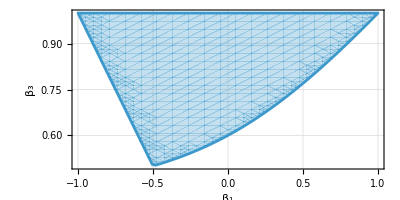

```mathematica
plt8=RegionPlot[cond2beta2/.κ->1,{β1,-1,1},{β3,1,1/2},AspectRatio->1/2,Frame->True,FrameLabel->{Subscript[β, 1],Subscript[β, 3]},LabelStyle->Directive[FontSize->12],RotateLabel->False,GridLines->Automatic]
```

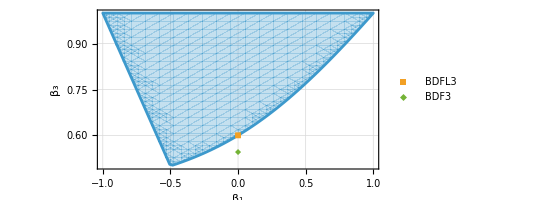

```mathematica
plt9=Show[plt8,plt6]
```

```mathematica
Export["3step_b1b3_examples.pdf",plt9]
```

3step_b1b3_examples.pdf

```mathematica
c32beta2[β1_,β3_]:=Module[
{a,b,sum},
a={-1-β1/2+(3 β3)/2,3-4 β3,-3+β1/2+(5 β3)/2,1};
b={0,β1,0,β3};
sum=Abs[1/(σ[b][1])Sum[(j^3 a[[j+1]])/(3!)-(j^(3-1)b[[j+1]])/((3-1)!),{j,0,Length[a]-1}]];
sum//Simplify
]
```

```mathematica
c32beta2[β1,β3]
```

1/6 Abs[(6+β1-11 β3)/(β1+β3)]

```mathematica
κlist2a=Table[{k,Quiet[Minimize[{c32beta2[β1,β3],cond2beta2/. κ->k},{β1,β3}][[1]]]},{k,0,1,1/100}];
```

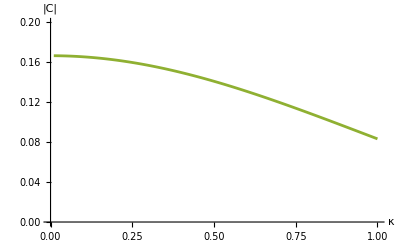

```mathematica
l3=ListLinePlot[κlist2a,AxesLabel->{κ, "|C|"},PlotRange->{{0,1},{0,1/5}},PlotStyle->ColorData[97][3],LabelStyle->Directive[FontSize->14]]
```

```mathematica
Export["3step_b1b3_examples_sc.pdf",l3]
```

3step_b1b3_examples_sc.pdf

### Finally, β_0 and β_3 are nonzero

```mathematica
cond2beta3=((3 Subscript[β, 3]==2&&-2/3<Subscript[β, 0]<2/3)||(11 Subscript[β, 3]==14&&6/11≤Subscript[β, 0]<14/11)||(6/11<Subscript[β, 3]<2/3&&6-10 Subscript[β, 3]≤Subscript[β, 0]<Subscript[β, 3])||(-2+2 Subscript[β, 3]≤Subscript[β, 0]<Subscript[β, 3]&&(2/3<Subscript[β, 3]<14/11||14/11<Subscript[β, 3]<2)))&&(Abs[Subscript[β, 0]]<Abs[κ^3 Subscript[β, 3]]&&Abs[Subscript[β, 0]^2-κ^6 Subscript[β, 3]^2]>0)/.{Subscript[β, 0]->β0,Subscript[β, 3]->β3}//Simplify;
```

```mathematica
c32beta3[β0_,β3_]:=Module[
{a,b,sum},
a={-1-(3 β0)/2+(3 β3)/2,3+2 β0-4 β3,-3-β0/2+(5 β3)/2,1};
b={β0,0,0,β3};
sum=Abs[1/(σ[b][1])Sum[(j^3 a[[j+1]])/(3!)-(j^(3-1)b[[j+1]])/((3-1)!),{j,0,Length[a]-1}]];
sum//Simplify
]
```

```mathematica
c32beta3[0,β3]
```

Abs[-11/6+1/β3]

```mathematica
κlist2b=Table[{k,Quiet[Minimize[{c32beta3[β0,β3],cond2beta3/. κ->k},{β0,β3}][[1]]]},{k,0,1,1/100}];
```

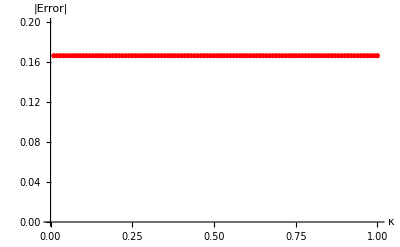

```mathematica
l4=ListPlot[κlist2b,AxesLabel->{κ, "|Error|"},PlotRange->{{0,1},{0,1/5}},PlotStyle->Red]
```

### Let’s now put it all together

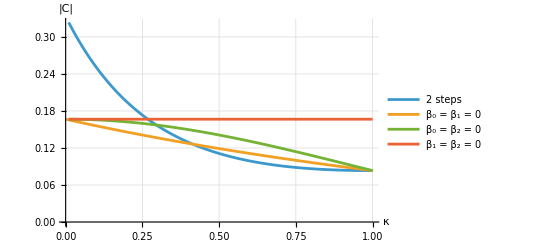

```mathematica
plt10=ListLinePlot[{κlist2,κlist,κlist2a,κlist2b},GridLines->Automatic,AxesLabel->{κ, "|C|"},PlotLegends->{"2 steps","β_0 = β_1 = 0","β_0 = β_2 = 0","β_1 = β_2 = 0"},LabelStyle->Directive[FontSize->14]]
```

```mathematica
Export["3step_twobetas_comparison.pdf",plt10]
```

3step_twobetas_comparison.pdf

### Let’s also show the RegionPlot for each set

```mathematica
Clear[sets]
```

```mathematica
eps=0.05;

sets=Evaluate[{cond2step&&Abs[β3]<eps,cond2beta&&Abs[β1]<eps,cond2beta2&&Abs[β2]<eps}/. κ->1];
```

```mathematica
RegionPlot3D[sets,{β1,-2,2},{β2,-2,2},{β3,0,2},AxesLabel->{Subscript[β, 1],Subscript[β, 2],Subscript[β, 3]},PlotLegends->{"2 steps",Subscript[β, 2]&&Subscript[β, 3]≠0,Subscript[β, 1]&&Subscript[β, 3]≠0},PlotPoints->100]
```

-Graphics3D-